# Atomic Nuclei

## Accepted Plots

### Equations

```mathematica
RAccepted[Energy_]:=412 Energy^(1.265-0.0954 Log[ⅇ,Energy]) (* Energy in MeV,RAccepted in mg *)
```

```mathematica
RAccepted2[Energy_]:=530 Energy-106(* Energy in MeV,RAccepted in mg *)
```

### Plots

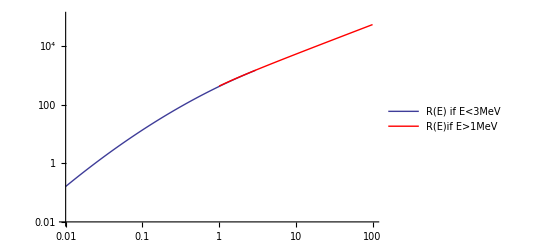

```mathematica
Show[LogLogPlot[RAccepted[Energylow],{Energylow,0.01,3},PlotRange->{{0.01,100},{0.01,100000}},PlotLegends->{"R(E) if E<3MeV"}],LogLogPlot[RAccepted2[Energy],{Energy,1,100},PlotRange->All,PlotStyle->Red,PlotLegends->{"R(E)if E>1MeV"}]]
```

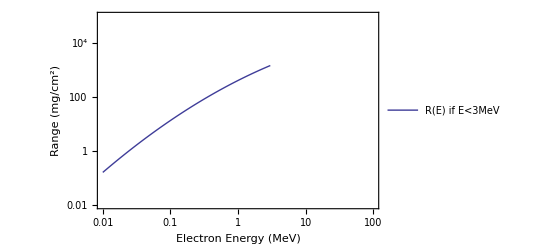

```mathematica
LogLogPlot[RAccepted[Energylow],{Energylow,0.01,3},PlotRange->{{0.01,100},{0.01,100000}},PlotLegends->{"R(E) if E<3MeV"} ,Frame->True,FrameLabel->{"Electron Energy (MeV)","Range (mg/cm^2)"},FrameStyle->{{FontSize->fontsize,FontFamily->fontfamily},{FontSize->fontsize,FontFamily->fontfamily}}]/.{fontfamily->"Times",fontsize->13}
```

### Calculations

```mathematica
peak1=RAccepted[0.624]/1000 (* Energy in MeV,RAccepted in g *)
```

0.222122

```mathematica
peak1/density/.density->2.70
```

0.0822673

## Aluminum

```mathematica
thicknessOfAl=0.0054; (* cm *)
```

```mathematica
energies={624.259601577,601,577.5,550.5,505.5,470.5,450.5};
```

```mathematica
thicknesses = Table[x thicknessOfAl,{x,0,Length[energies]-1}];
```

```mathematica
data=Transpose[{energies,thicknesses}];
```

```mathematica
data//MatrixForm
```

(624.26 | 0.
601 | 0.0054
577.5 | 0.0108
550.5 | 0.0162
505.5 | 0.0216
470.5 | 0.027
450.5 | 0.0324)

```mathematica
line=Fit[data, {1,x},x]
```

0.110668-0.000174951 x

```mathematica
errorsAl={3,4,1.5,7.5,1.5,8.5,10.5};
```

```mathematica
aluminumDistanceFunctionOfEnergy=LinearModelFit[data,x,x,Weights->1/errorsAl^2]
```

FittedModel[0.106876-0.000167932 x]

```mathematica
Solve[aluminumDistanceFunctionOfEnergy[0]==dm,dm]
```

{{dm→0.106876}}

```mathematica
Plot[line[x],{x,0,700},PlotStyle->{Blue}]
```

-Graphics-

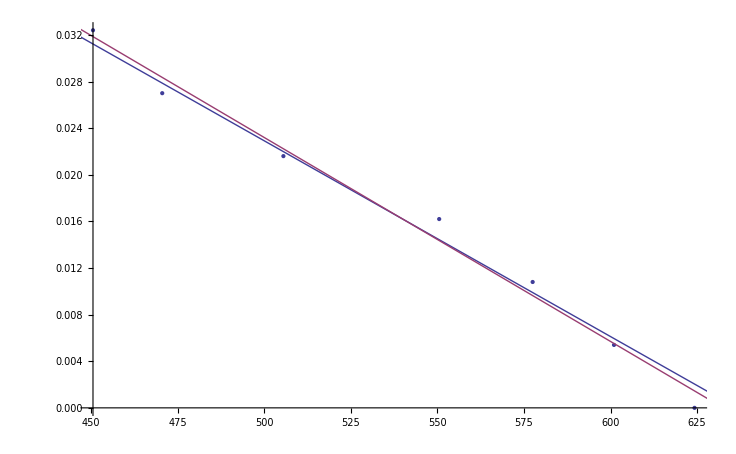

```mathematica
Show[{ListPlot[data],Plot[{aluminumDistanceFunctionOfEnergy[x],line},{x,0,700}]}]
```

## Plastic

```mathematica
thicknessOfPlastic=0.01; (* cm *)
```

```mathematica
energiesOfPl={624.259,591.5,567.5,537.5,501,470.5,413};
```

```mathematica
thicknessesPl ={0.,0.01,0.02,0.03,0.04,0.05,0.07}
```

{0.,0.01,0.02,0.03,0.04,0.05,0.07}

```mathematica
dataPl={energiesOfPl,thicknessesPl};
```

```mathematica
Transpose[dataPl]//MatrixForm
```

(624.259 | 0.
591.5 | 0.01
567.5 | 0.02
537.5 | 0.03
501 | 0.04
470.5 | 0.05
413 | 0.07)

```mathematica
line=Fit[Transpose[dataPl], {1,x},x]
```

0.205466-0.000328793 x

```mathematica
EnergyAsFunctionOf[x_]:=0.20546613374720163-0.00032879292277015207 x
```

```mathematica
Solve[EnergyAsFunctionOf[0]==x,x] (* Gives Distance in cm to stop electron to zero in Plastic *)
```

{{x→0.205466}}

```mathematica
errorPl={3,6.5,5.5,6.5,9,4.5,13}
```

{3,6.5,5.5,6.5,9,4.5,13}

```mathematica
lm=LinearModelFit[Transpose[dataPl],x,x,Weights->1/errorPl^2]//Normal
```

0.204748-0.000327697 x

```mathematica
lm[{"BestFit","ParameterTable"}]
```

(0.204748-0.000327697 x)[{BestFit,ParameterTable}]

```mathematica
fitWithErrors[x_]:=0.2047476945240543-0.000327696558898258 x
```

```mathematica
Solve[fitWithErrors[0]==x,x]
```

{{x→0.204748}}

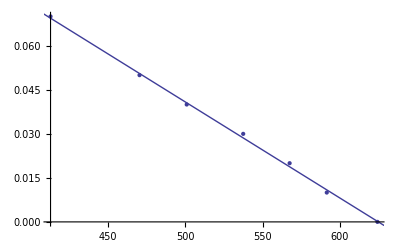

```mathematica
Show[{ListPlot[Transpose[dataPl]],Plot[fitWithErrors[x],{x,0,700}]}]
```